```mathematica
phisup[x_]:=Max[0,Min[1,2 x],Min[2,x]]
```

```mathematica
phiminmod[y_]:=Max[0,Min[1,y]]
```

```mathematica
phiMC[x_]:=Max[0,Min[0.5(1+x),2,2 x]]
```

```mathematica
phiVanLeer[x_]:=(x+Abs[x])/(1+Abs[x])
```

```mathematica
Subscript[y, 1][x_]:=Min[1,x]
```

```mathematica
Subscript[y, 2][x_]:=Min[2,2x]
```

```mathematica
Subscript[y, 2][x]
```

Min[2,2 x]

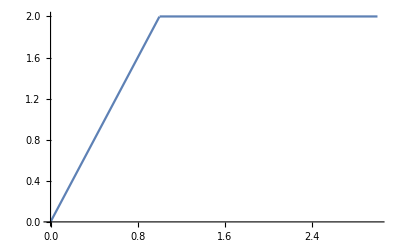

```mathematica
Plot[Min[2,2 x],{x,0,3}]
```

```mathematica
phiLW[x_]:=Min[1,2x]
```

```mathematica
phiBW[x_]:=Min[2,x]
```

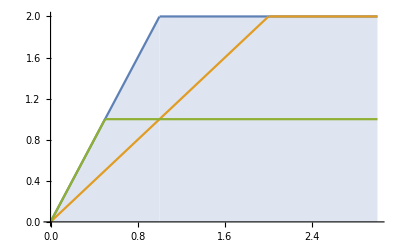

```mathematica
Plot[{Subscript[y, 2][x],phiBW[x],phiLW[x]},{x,0,3},Filling->{1->Axis}]
```

```mathematica
phiSper[x_]:=(1/3+2/3 x)(3 x^3-2 x^2+3x)/(2 x^4+2)
```

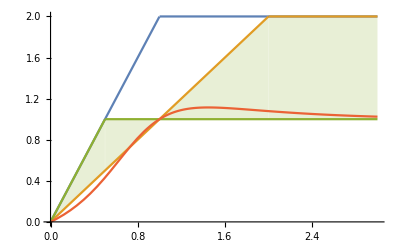

```mathematica
Plot[{Subscript[y, 2][x],phiBW[x],phiLW[x],phiSper[x]},{x,0,3},Filling->{3->{2}}]
```

```mathematica
phiKoren[x_]:=Max[0,Min[2x,(2+x)/3,2]]
```

```mathematica
phiKoren[x]
```

Max[0,Min[2,2 x,(2+x)/3]]

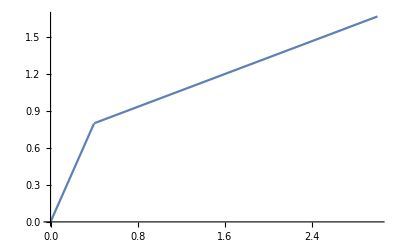

```mathematica
Plot[Max[0,Min[2,2 x,(2+x)/3]],{x,0,3}]
```

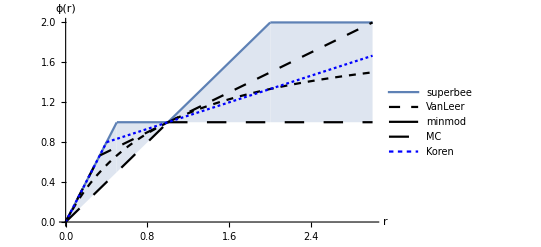

```mathematica
Plot[{phisup[x],phiVanLeer[x],phiminmod[x],phiMC[x],phiKoren[x]},{x,0,3},Filling->{1->{3}},PlotLegends->{superbee,VanLeer,minmod,MC,Koren},AxesLabel->{HoldForm[r],HoldForm[ϕ[r]]},PlotStyle->{Dashing[Line],{Dashing[Small],Black},{Dashing[Large],Black},{Dashing[Medium],Black},{Dashing[Tiny],Blue}}]
```